Шумы при сдвиге частот Δφ=0:
Через функции!

```mathematica
Unprotect[Internal`EncodeCharacters];

Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]

SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma_bac\PCA

```mathematica
SVDVector[x_, a_?NumberQ] := Transpose[SingularValueDecomposition[x][[1; 3]]][[a]];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],PlotRange->All,PlotStyle->Red,FrameLabel->{"ν","A, mm"}]
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->12,Bold},ImageSize->600,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
sig1=Table[Cos[2 π *0.03* k] +3(Random[]-0.5),{k,1,500}];
sig2=Table[0.8*(Cos[2 π *0.03* k] +3(Random[]-0.5)),{k,1,500}];
sig3=Table[0.95*(Cos[2 π *0.03* k] +3(Random[]-0.5)),{k,1,500}];
sig4=Table[0.85*(Cos[2 π *0.03* k] +3(Random[]-0.5)),{k,1,500}];
SigM=Transpose[{{sig1},{sig2},{sig3},{sig4}}];
```

0.03

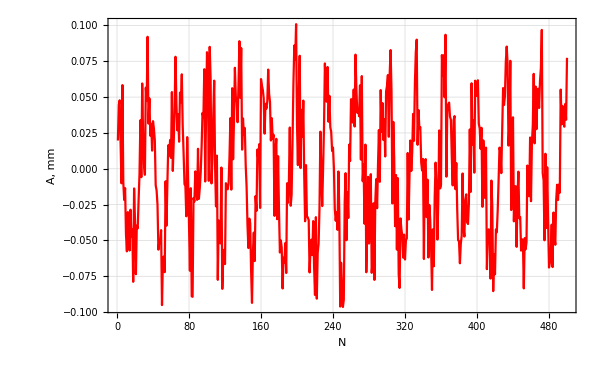

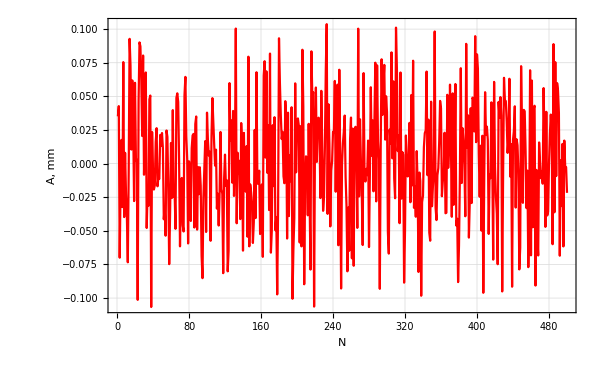

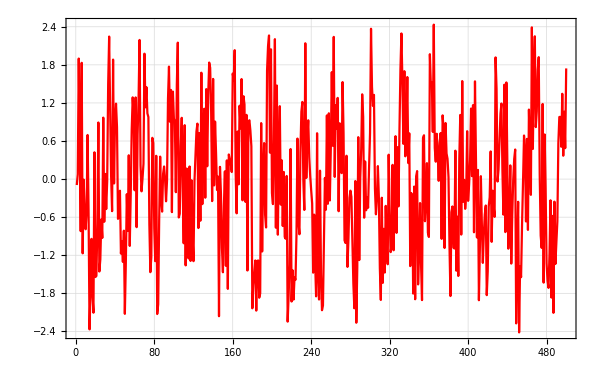

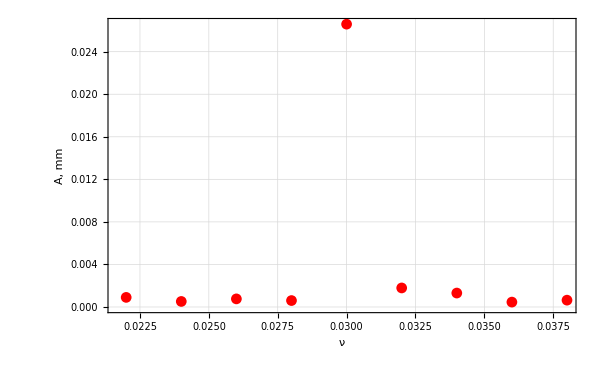

```mathematica
SVDVector1=SVDVector[SigM,1];
SVDVector2=SVDVector[SigM,2];
Freq[SVDVector1]
SVDPlot1=ListPlot[SVDVector1,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
SVDPlot2=ListPlot[SVDVector2,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
sigPlot=ListPlot[sig1,Joined->True,PlotRange->All]
TrueSVD1=TruePlot[SVDVector1]
```

0.168

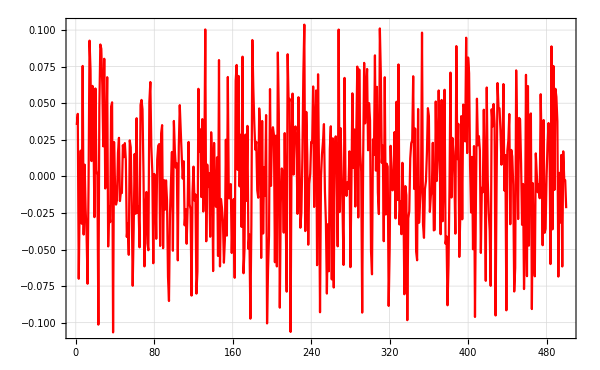

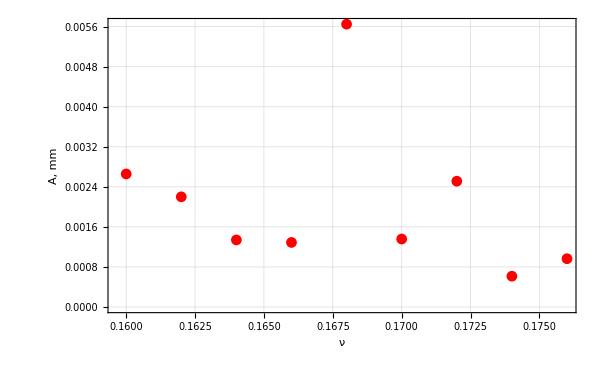

```mathematica
SVDVector2=SVDVector[SigM,2];
Freq[SVDVector2]
ListPlot[SVDVector2,Joined->True,PlotRange->All]
TrueSVD2=TruePlot[SVDVector2]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma_bac\PCA

Export["SigPlot.png",sigPlot]
Export["PCA1.png",SVDPlot1]
Export["PCA2.png",SVDPlot2]
Export["Spec1.png",TrueSVD1]
Export["Spec2.png",TrueSVD2]

SigPlot.png

PCA1.png

PCA2.png

Spec1.png

Spec2.png

0.012

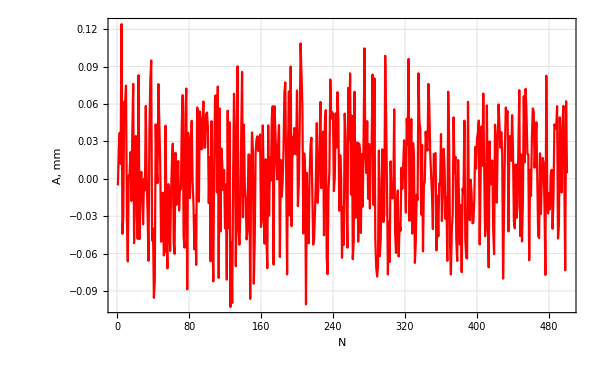

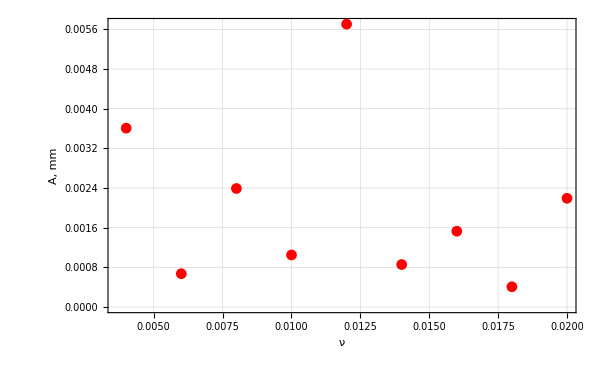

```mathematica
SVDVector4=SVDVector[SigM,4];
Freq[SVDVector4]
SVDPlot4=ListPlot[SVDVector4,Joined->True,PlotRange->All,FrameLabel->{"N","A, mm"}]
TrueSVD4=TruePlot[SVDVector4]
```

```mathematica
Export["SVDPlot4.png",SVDPlot4]
Export["TrueSVD4.png",TrueSVD4]
```

SVDPlot4.png

TrueSVD4.png

0.03

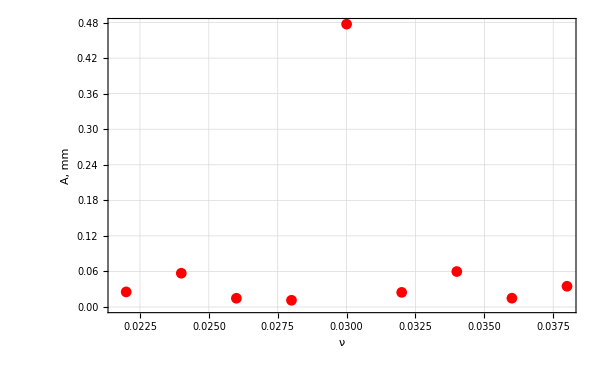

```mathematica
Freq[sig1]
Truesig=TruePlot[sig1]
```

```mathematica
Export["Truesig.png",Truesig]
```

Truesig.png

```mathematica
image = {{SVDPlot1,TrueSVD1,SVDPlot2, TrueSVD2}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
(*Export["SVDEx.png", image]*)
```

SVDEx.png